# Minimum Inventory, Maximum Diversity

MonthName Day, Year

Chris Carlson, User Interface Group

Q: What do proteins, snowflakes, and these figures have in common?

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

A: They're all instances of "minimum inventory/maximum diversity" systems, a term coined by Peter Pearce in his book, Structure in Nature Is a Strategy for Design (MIT Press, 1978).

A minimum inventory/maximum diversity system is a kit of modular parts and rules of assembly that gives you maximal design bang for your design- component buck. It's a system that achieves a wide variety of effects from a small variety of parts. Nature excels at this game: every one of the many millions of natural proteins is assembled from an inventory of just 20 amino acids. Snowflakes are all just arrangements of the humble water molecule, H_2O.

The same idea applies to the forms in the figure above, which are all constructed from semicircles joined at connection points evenly distributed along a vertical line. I stumbled onto this minimum inventory/maximum diversity system while playing with logo designs for a previous blog post, Exploring Logo Designs with Mathematica. The idea came from a logo for a concert hall by Peter Andermatt, approximated here:

In my previous post, I was exploring parametric variations of logo designs in Mathematica. Although this concert-hall logo is trivially easy to parameterize and get into Mathematica, I nearly didn't try doing so because I didn't think that the exploration would lead anywhere interesting. So much for my intuition. Relative to its simplicity, the idea of joining semicircles at fixed points along a line is one of the richest and most expressive component systems that I've run across. That becomes apparent once you build a widget to explore the concept.

Not wanting to invest much effort in something that I thought wouldn't be productive, I dashed off a widget that hooked up sliders to the y-coordinate values of the endpoints of the semicircles:

```mathematica
Manipulate[
Graphics[{Thickness[th], CapForm["Butt"], 
    Table[Module[{
ya=(2/(n-1))({l1a,l2a,r1a,r2a,r3a}[[i]])-1,
yb=(2/(n-1))({l1b,l2b,r1b,r2b,r3b}[[i]])-1},
Circle[{0,(ya+yb)/2},Abs[ya-yb]/2,If[i<=2,{90,270}°,{-90,90}°]]],{i,1,5}]
},PlotRange->1.1,ImageSize->260],
{{n,15,"n points"},2,20,1},
{{th,.04,"thickness"},0,.2},
Row[{
Control[{{l1a,0},0,20,1,ImageSize->Small}],Control[{{l1b,14},0,20,1,ImageSize->Small}]
}],...]
```

This is what I saw as I began to twiddle the sliders:

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | ...

Nothing astounding here, but at this early point two things became apparent: (1) there was more out there to explore than I had expected, and (2) it would be worth my while to invest effort in a better widget to explore it with. My quick-and-dirty widget had done its job: it pointed the way toward something more interesting. If it hadn't been so easy to construct, I probably wouldn't have made it, and I would have passed right by the elegantly simple system I'm about to describe. This is one of the strengths of Mathematica: you can do things on a whim that with other systems would require so much effort that they wouldn't be worth your while. And so you miss opportunities to discover new things.

I designed a more usable widget (using the Locator function) that let me drag the semicircles directly and add and remove semicircles by command-clicking on a Mac (alt-clicking for Windows). I also gave myself more control over the details of how the forms are rendered. This took more thought than my initial attempt, particularly in understanding how to constrain the locators so that the endpoints of the semicircles land on the connection points. Nevertheless, I had the new exploration widget refined and running in about 20 minutes. I think it has an impressively high ratio of functionality to volume of code.

```mathematica
Manipulate[
Graphics[{AbsoluteThickness[th],CapForm[caps],
Rotate[{
pts=RotationTransform[45°][Round[#,√(.5)]&/@
RotationTransform[-45°][#]]&/@pts;
Circle[{0,#[[2]]},Abs[#[[1]]],If[#[[1]]<0,{90°,270°},{-90°,90°}]]&/@pts
},angle °,{0,0}]},PlotRange->(n+2)/2],
{{n,9,"connection points"},3,24,1},
{{th,4.6,"thickness"},1,100},
{{angle,0,"orientation"},0,360,1},
{{caps,"Round","endcaps"},{"Butt","Round"}},
{{pts,{{2,1},{-1.5,-1.5},{-1,0},{1,2},{1.5,1.5}}},-5{1,1},5{1,1},Locator,LocatorAutoCreate->True,Appearance->None}
]
```

Now I was off and running through this space of designs, and discovering all sorts of intriguing forms. The more I explored, the more I wanted to explore:

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | ...

I began to notice recurring themes—the idioms of this design language—such as spirals, wormy forms, and the comma-shaped Fischblase or mouchette found in Gothic window traceries:

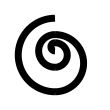
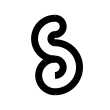
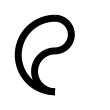

To get a better overview of the material I had to work with, I decided to do some exhaustive generation of forms. For that, I needed a representation of forms and a function for rendering it. I settled on an ArcForm expression whose arguments are the list of y-coordinate values of the connection points, and lists of endpoint indices for the left and right arcs. Here is an example:

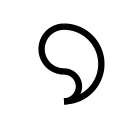

```mathematica
Render[ArcForm[{0,2,5}, {{2,3}}, {{1,2},{1,3}}]]
```

With this representation, writing a function that generates all of the forms with a given number of connection points is straightforward and concise. The function forms all pairs of connection points, then all subsets of the pairs, then all pairs of the subsets. Every possible arc form is contained in those combinations.

```mathematica
ArcForms[n_]:=
Module[{allArcs = Subsets[Range[1,n],{2}]},
Flatten[Outer[ArcForm[Range[1,n], #1,#2]&, Subsets[allArcs],Subsets[allArcs],1],1]
]
```

Now I could begin to see in a systematic way what's out there. With two connection points, there are four possible forms (one of which, with 0 left arcs and 0 right arcs, is empty):

```mathematica
Row[Render/@ ArcForms[2]]
```

-Graphics--Graphics--Graphics--Graphics-

With three connection points, that number goes up to 64. This figure is the beginning of a useful catalog of the basic vocabulary of this design language:

```mathematica
Grid[Partition[Render /@ ArcForms[3],8]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

From there the number of forms grows so quickly that after three connection points it is no longer practical to render them all. A back-of-the-envelope Mathematica calculation shows just how quickly. There are Binomial[n,2] possible two-element subsets of n objects—the number of different arcs available for each side of a form with n connection points. There are 2^Binomial[n,2] ways of taking subsets of that set—the number of arc combinations available for each side. And the square of that number gives the total number of distinct forms, as each form combines one member of that set on the left side with one member on the right side. Thus the total number of forms with n connection points is

```mathematica
(2^Binomial[n,2])^2
```

2^((-1+n) n)

How quickly that number rises is graphically evident in this table:

n | number of arc forms
2 | 4
3 | 64
4 | 4096
5 | 1048576
6 | 1073741824
7 | 4398046511104
8 | 72057594037927936
9 | 4722366482869645213696
10 | 1237940039285380274899124224
11 | 1298074214633706907132624082305024
12 | 5444517870735015415413993718908291383296

With a modest eight connection points, a figure showing all possible forms drawn at the scale of the figure above would almost exactly cover North America. Imagine crisscrossing the continent from Panama to Alaska to Greenland on your hands and knees, nose to the ground, searching for forms! No, really try to imagine that! Think about how huge a task exploring a figure the size of a mere soccer field would be. Now think about crawling around your entire city. Extrapolate to your continent. Such is the magnitude of the search task, an immensity that you're hardly aware of when such large numbers are hidden behind the buttons and sliders of an exploration widget. From here on out, this was the central problem I grappled with: how grasp the possibilities within this ungraspably large space of designs.

Now my adventure became both exploration and meta-exploration. At the same time I was exploring the design space, I was exploring how best to explore the design space. Mathematica's trivially-easy-to-use interface constructs made it possible for me to try out and discard a number of widget possibilities before I arrived at a combination that worked well for the amount of effort I was willing to invest. I tried "scrubbing" through entire design spaces using sliders, random sampling of various sorts, and several methods of presenting samples.  What I arrived at is a pair of widgets that work together: a "discovery" widget for sampling the design space, and a "design" widget for developing particular forms that I picked out of the design space.

This is the discovery widget (click for an enlarged view):

-Graphics-

The discovery widget implements a "generate-and-test" paradigm: it randomly generates forms with a given number of connection points and left and right arcs, and selects those that meet given criteria. Each press of the "more" button gives a new sample, whose size I can control. By displaying many forms at once, I get an aerial view of the design space and can cover territory more quickly.

The selection criteria are implemented as filter functions that given an ArcForm return True (retain) or False (reject). Here is the filter for forms that contain at least one circle. It tests that there is some member of the left arcs that also occurs in the right arcs. Such a pair forms a circle.

```mathematica
SomeCircleFilter[ArcForm[ys_,la_,ra_]]:=
Or @@(MemberQ[ra,#]& /@ la)
```

I wrote additional filters for rotational symmetry, forms that are enclosed in an outer circle,  forms with limited arc radii, and so on. I designed the filter portion of the widget so that I could easily drop in new filters as they occurred to me.

The last section of controls in the widget let me choose how the forms are rendered. Depending on what graphical phenomenon I'm interested in, I may want to see thick or thin lines, butt or round end caps, black-on-white or white-on-black.

With this widget, I sampled spaces of increasingly complex forms, pulling out some that I thought gave the illusion of design intention; that is, that appeared to show evidence of a  human hand. This is what I found:

5 connection points, 1 left arc, 2 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

5 connection points, 2 left arcs, 2 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

6 connection points, 1 left arc, 2 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

6 connection points, 2 left arcs, 2 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

6 connection points, 3 left arcs, 2 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

8 connection points, 3 left arcs, 4 right arcs:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

One of the more interesting filters is the one for rotational symmetry. Turning it on yields forms that remind me of traditional printer's embellishments...

-Graphics--Graphics--Graphics--Graphics-

...as well as some non-traditional candidates.

-Graphics--Graphics--Graphics--Graphics-

Rotational symmetry also yields a practically inexhaustible supply of "S" logos. Most are unlikely to win a beauty contest, and they tend to have a forties or fifties design vibe. But each is interesting in its own right, and together they are a reminder of how very many variations there can be on a single theme.

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | ...

Some of the generate-and-test filters are fantastically inefficient. A rotational-symmetry-with-maximum-arc-diameter-2 filter that I used while exploring the printer's embellishments rejects upwards of 2000 forms for every one that it accepts. But who cares! It's fantastically efficient for me. The scheme was easy to implement, and I was able to get down to the real work of exploring quickly. The typical laptop is capable of generating and testing half a million forms in the amount of time I'm willing to wait after clicking the "more" button.

The second component of my exploration tools—the "design" widget—pops up when you click one of the forms in the discovery widget. It provides a way of exploring a single form in detail. The design widget has the same rendering controls as the discovery widget, but also lets you drag arcs and connection points in order to fine-tune or improvise on forms. I also added a "negate" setting that renders the negative spaces between the arcs rather than the arcs themselves. The shapes of those forms had intrigued me while I was exploring the design space. Here's a snapshot of the complete design widget:

Using the discovery and design widgets together is a little like beachcombing. You wander around the design space looking for interesting forms or something that sparks an idea. When you find one, you toss it into the design widget for tweaking or exploration of related forms. Here is a snapshot of some informal exploration I did. Each row of forms begins with a form picked from the discovery widget, and proceeds through an exploration in the design widget.

-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

You can try out the discovery and design widgets yourself by downloading the Demonstrations Arc Form Discovery Widget and Arc Form Design Widget. You may discover, as I have, that in design, constraint is freedom. Picasso put it this way: “Forcing yourself to use restricted means is the sort of restraint that liberates invention. It obliges you to make a kind of progress that you can’t even imagine in advance.” I wholeheartedly agree.

## Implementation

### Render

```mathematica
ClearAll[Render]
```

```mathematica
RenderingPlotRange[ArcForm[ys_,la_, ra_]]:=
Module[{xMin,xMax,yMin,yMax},
yMin=Min[ys]-1;
yMax=Max[ys]+1;
If[yMin===yMax, yMin=-1;yMax=1];
xMin = -(yMax-yMin-2)/2 - 1;
xMax = -xMin;
N[{{xMin, xMax},{yMin,yMax}}]
]
```

```mathematica
Render[arcForm:ArcForm[ys_,la_, ra_],opts___]:=
Module[{
thickness = Thickness /. {opts} /. {Thickness->.25}, (* user units *)
roundCaps = RoundCaps/.{opts}/.{RoundCaps->True}, (* True->"Round", False->"Butt" *)
orientation = Orientation/.{opts}/.{Orientation->0}, (* clockwise rotation from vertical, degrees *)
invert = Invert /. {opts}/.{Invert -> False}, (* True -> swap black and white *)
negate = Negate/.{opts}/.{Negate->False}, (* True -> swap foreground and background: focus on negative spaces *)
pixelsPerUnit = Scale/.{opts}/.{Scale->50}, (* pixels per user unit *),
showPoints = ShowPoints/.{opts}/.{ShowPoints->False},
xMin,xMax,yMin,yMax,
imageWidth, imageHeight,foreground,background
},
{{xMin, xMax},{yMin,yMax}}=RenderingPlotRange[arcForm];
foreground = If[invert,White,Black];
background = If[invert, Black,White];
Graphics[{
Thickness[thickness/(xMax-xMin)],
CapForm[If[roundCaps,"Round","Butt"]],
Rotate[{
If[negate,{
FaceForm[foreground],EdgeForm[{foreground,AbsoluteThickness[1]}],
Disk[{0,(ys[[#[[1]]]]+ys[[#[[2]]]])/2.},Abs[ys[[#[[1]]]]-ys[[#[[2]]]]]/2.,{90,270}°]& /@ la,
Disk[{0,(ys[[#[[1]]]]+ys[[#[[2]]]])/2.},Abs[ys[[#[[1]]]]-ys[[#[[2]]]]]/2.,{-90,90}°]& /@ ra
},{}
],
{If[negate,background,foreground],
Circle[{0,(ys[[#[[1]]]]+ys[[#[[2]]]])/2.},Abs[ys[[#[[1]]]]-ys[[#[[2]]]]]/2.,{90,270}°]& /@ la,
Circle[{0,(ys[[#[[1]]]]+ys[[#[[2]]]])/2.},Abs[ys[[#[[1]]]]-ys[[#[[2]]]]]/2.,{-90,90}°]& /@ ra
},
If[showPoints, {Gray,AbsolutePointSize[5],Point[{0,#}& /@ ys]},{}]
},-orientation,{xMax+xMin,yMax+yMin}/2.]},
PlotRange->{{xMin,xMax},{yMin,yMax}},ImageSize->{(xMax-xMin), (yMax-yMin)}pixelsPerUnit,
Background->background]
];
```

```mathematica
Manipulate[
Render[ArcForm[{0,1,2,3,4,5,6},{{1,2},{1,3},{1,7}},{{1,3},{2,3},{1,4}}],
Scale->scale,
RoundCaps->roundCaps,
Orientation->orientation,
Negate->negate,
Invert->invert,
Thickness->thickness,
ShowPoints->showPoints
],
{{scale,30},0,50},
{{roundCaps,True},{True,False}},
{{orientation,0},0,360},
{{negate,False},{True,False}},
{{invert,False},{True,False}},
{{thickness,.5},0,2},
{{showPoints,False},{True,False}}
]
```

### Discovery Interface

```mathematica
ArcFormsCount[np_,nl_,nr_]:=Binomial[Binomial[np,2],nl]Binomial[Binomial[np,2],nr]
```

```mathematica
ArcFormRandom[np_, nl_, nr_]:=
Module[{allArcs = Subsets[Range[1,np],{2}]},
ArcForm[Range[1,np],Sort[RandomSample[allArcs,nl]],Sort[RandomSample[allArcs,nr]]]
]
```

```mathematica
OuterCircleFilter[ArcForm[ys_,la_,ra_]]:=
Module[{n=Length[ys]},MemberQ[la,{1,n}]&&MemberQ[ra,{1,n}]]
```

```mathematica
RotationalSymmetryFilter[ArcForm[ys_,la_,ra_]]:=
With[{n=Length[ys]+1},la===Sort[Sort[(n{1,1}-#)]& /@ ra]]
```

```mathematica
TopBottomSymmetryFilter[ArcForm[ys_,la_,ra_]]:=
With[{n=Length[ys]+1},
And@@(MemberQ[la,Sort[(n{1,1}-#)]]&/@ la) && And@@(MemberQ[ra,Sort[(n{1,1}-#)]]&/@ ra)
]
```

```mathematica
NoCircleFilter[arcForm:ArcForm[ys_,la_,ra_]]:=
!SomeCircleFilter[arcForm]
```

```mathematica
SomeCircleFilter[ArcForm[ys_,la_,ra_]]:=
Or @@(MemberQ[ra,#]& /@ la)
```

```mathematica
MaxDiameterFilter[ArcForm[ys_,la_,ra_],d_]:=
And@@((Abs[First[#]-Last[#]]≤d)&/@ Join[la,ra])
```

```mathematica
DiscoverArcForms[]:=Manipulate[
trigger;nHits=0; nTries=0;
nl = Min[nl,np(np-1)/2];
nr = Min[nr,np(np-1)/2];
Grid[Table[
With[{arcForm = Module[{try=ArcFormRandom[np,nl, nr]},
nTries++;
While[!filter[try], nTries++; try=ArcFormRandom[np,nl, nr]];
nHits++;try]},
Button[
Dynamic[Render[arcForm,
Scale->320./√ss/np,
RoundCaps->roundCaps,
Orientation->orientation °,
Negate->negate,
Invert->invert,
Thickness->thickness,
ShowPoints->showPoints
]],
Print[ExploreArcForm[arcForm,
Scale->30,
RoundCaps->roundCaps,
Orientation->orientation °,
Negate->negate,
Invert->invert,
Thickness->thickness,
ShowPoints->True]],
Appearance->None,Method->"Queued"
]],{√ss},{√ss}],Background->Dynamic[If[invert,Black,White]],Spacings->0],
{{trigger,0},ControlType->None},
{{nHits,1},ControlType->None},
{{nTries,1},ControlType->None},
{{spacer,Style["xxxxxxxxxxxxx",White]},ControlType->None},
{{np,6},ControlType->None},
{{nl,3},ControlType->None},
{{nr,3},ControlType->None},
{{ss,16},ControlType->None},

Button["more",trigger++],
Dynamic[ProgressIndicator[N[nHits/ss]]],
Delimiter,
Style["Forms",Bold],
Grid[{
{"n points", Slider[Dynamic[np],{2,12,1},ImageSize->Small],Dynamic[np]},
{"n left arcs", Slider[Dynamic[nl ],{0,12,1},ImageSize->Small],Dynamic[nl]},
{"n right arcs", Slider[Dynamic[nr],{0,12,1},ImageSize->Small],Dynamic[nr]},
{"",Row[{"(",Dynamic[ArcFormsCount[np,nl,nr]]," possible forms)"}],},
{"sample size", SetterBar[Dynamic[ss],{4,16,36,64,100}],}
},Alignment->{{Right,{Left}},Automatic}],

Delimiter,
Style["Filter",Bold],
{{filter,True&},ControlType->None},
Grid[{
{" ",With[{np=np},PopupMenu[Dynamic[filter],{
True&->Style["None",10],
Delimiter,
RotationalSymmetryFilter->Style["Rotational Symmetry",10],
(RotationalSymmetryFilter[#] && MaxDiameterFilter[#,2])& ->Style["Rotational Sym, Max Dia 2",10],
(RotationalSymmetryFilter[#] && MaxDiameterFilter[#,3])& ->Style["Rotational Sym, Max Dia 3",10],
TopBottomSymmetryFilter->Style["Top-Bottom Symmetry",10],
Delimiter,
OuterCircleFilter->Style["Outer Circle",10],
SomeCircleFilter->Style["Some Circle",10],
NoCircleFilter->Style["No Circle",10],
Delimiter,
MaxDiameterFilter[#,2]& ->Style[ "Max Diameter 2",10],
MaxDiameterFilter[#,3]& ->Style[ "Max Diameter 3",10]
}]]},
{" ",Dynamic[Row[{" tests per hit: ",If[nHits===0,nTries,Round[nTries/nHits]]}]]}
},Alignment->{{Right,{Left}},Automatic}],

Delimiter,
Item[Style["Rendering",Bold]],
Item[Grid[{
{Control[{{thickness,.25,"thickness"},0,2,ImageSize->Small}],},
{Control[{{orientation,0,"orientation"},0,360,ImageSize->Small}],},
{Control[{{roundCaps,True,"round caps"},{True,False}}],Control[{{negate,False,"negate"},{True,False}}]},
{Control[{{showPoints,False,"show points"},{True,False}}],Control[{{invert,False,"invert"},{True,False}}]}
},Alignment->Right]],
TrackedSymbols:>{np,nl,nr,filter,trigger,thickness,roundCaps,orientation,negate,showPoints,ss},
ControlPlacement->Left,SaveDefinitions->True
]
```

### Design Interface

```mathematica
ViewTransform[arcForm_, orientation_]:=
Module[{xMin,xMax,yMin,yMax,center},
{{xMin,xMax},{yMin,yMax}} = RenderingPlotRange[arcForm];
center = {xMin+xMax,yMin+yMax}/2.;
RotationTransform[orientation,center]
];
```

```mathematica
GetHit[pt_,arcForm:ArcForm[ys_,la_,ra_], thickness_]:=
Module[{i, minDist,minHitDist=thickness/2.,arcs,hitAngle},

(* First test for connection point hits *)
i=0;
minDist=$MaxMachineNumber;
MapIndexed[Module[{dist=Abs[Norm[pt-{0,#}]]},If[dist<minDist,i=First[#2];minDist=dist]]& , ys];
If[minDist < minHitDist,Return[{1,i}]];

(* Then test for arc hits*)
minDist=$MaxMachineNumber;
arcs=If[First[pt]<0,la,ra];
i=0;
MapIndexed[Module[{dist=Abs[Norm[pt-{0,(ys[[First[#]]]+ys[[Last[#]]])/2}]-Abs[ys[[First[#]]]-ys[[Last[#]]]]/2]},If[dist<minDist,i=First[#2];minDist=dist]]& , arcs];
If[minDist < minHitDist,
hitAngle = ArcTan@@(pt-{0,(ys[[arcs[[i,1]]]]+ys[[arcs[[i,2]]]])/2});
If[Abs[hitAngle] > π/2, hitAngle =Sign[hitAngle]( π-Abs[hitAngle])];
{If[First[pt]<0,2,3],i, Sign[hitAngle]},
(* Else *)
$Failed
]
]
```

```mathematica
NearestIndex[ys_, y_]:=
Position[ys, First[Nearest[ys,y]]][[1,1]]
```

```mathematica
Drag[arcForm_ArcForm, $Failed, ___]:=
arcForm
```

```mathematica
Drag[arcForm:ArcForm[ys_,la_,ra_], {1,i_}, p0_,p1_]:=
ArcForm[ReplacePart[ys,i->Last[ys[[i]] + p1-p0]],la,ra]
```

```mathematica
OtherY[y0_, {x_,y_}]:=
Module[{r=Abs[(x^2+y^2-2 y y0+y0^2)/(2 (-y+y0))],yc=(x^2+y^2-y0^2)/(2 (y-y0))},
If[y<y0,yc-r,yc+r]
]
```

```mathematica
Drag[arcForm:ArcForm[ys_,la_,ra_], {lr:2|3,i_, j_}, p0_,p1_]:=
Module[{arcs,y1,y2,k,yNearest,v=p1-p0,newForm},

(* Figure out which index is being dragged *)
arcs=arcForm[[lr]];
y1=ys[[arcs[[i,1]]]];
y2=ys[[arcs[[i,2]]]];
(* k is the index (1 or 2) of the side of the arc being dragged *)
k=If[y1 < y2&&j<0 || y1≥y2&&j≥0,1, 2];

(* Map dragged endpoint to nearest connection point *)
newForm = ReplacePart[arcForm,{lr,i,k}->NearestIndex[ys, OtherY[ys[[arcs[[i,3-k]]]],p1]]];
If[Sign[p0[[1]]]=!=Sign[p1[[1]]], (* flip arc to the other side *)
newForm = Delete[Insert[newForm,newForm[[lr,i]],{5-lr,-1}],{lr,i}]
];
newForm
]
```

```mathematica
AddArc[arcForm:ArcForm[ys_,la_,ra_],pt_]:=
Module[{newArc},
newArc = NearestIndex[ys,#]&/@{pt[[2]]-Abs[pt[[1]]],pt[[2]]+Abs[pt[[1]]]};
ArcForm[ys, 
If[pt[[1]]<0,Union[la,{newArc}],la],
If[pt[[1]]≥0,Union[ra,{newArc}],ra]]
]
```

```mathematica
AddPoint[arcForm:ArcForm[ys_,la_,ra_],pt_]:=
ArcForm[Append[ys,pt[[2]]],la,ra]
```

```mathematica
DeleteArc[arcForm:ArcForm[ys_,la_,ra_], {lr:2|3,i_, _}]:=
Delete[arcForm,{lr,i}]
```

```mathematica
DeletePoint[arcForm:ArcForm[ys_,la_,ra_], i_]:=
Module[{y=ys[[i]]},
ArcForm[Delete[ys,i],
Map[If[#≥i, #-1,#]&,Select[la,(!MemberQ[#,i])&],{-1}],
Map[If[#≥i, #-1,#]&,Select[ra,(!MemberQ[#,i])&],{-1}]]
]
```

```mathematica
RespacePoints[arcForm:ArcForm[ys_,la_,ra_]]:=
Module[{newYs=Range[Min[ys],Max[ys],(Max[ys]-Min[ys])/(Length[ys]-1)]},
ArcForm[newYs[[
Last /@ Sort[Thread[Ordering[ys]->Range[Length[ys]]]]
]],la,ra]
]
```

```mathematica
ExploreArcForm[arcFormIn:ArcForm[ys_,la_,ra_], opts___] :=
With[{
scale0=Scale/.{opts}/.{Scale->30},
roundCaps0=RoundCaps/.{opts}/.{RoundCaps->True},
orientation0=Orientation/.{opts}/.{Orientation->0},
negate0=Negate/.{opts}/.{Negate->False},
invert0=Invert/.{opts}/.{Invert->False},
thickness0=Thickness/.{opts}/.{Thickness->.25},
showPoints0=ShowPoints/.{opts}/.{ShowPoints->True}
},
Manipulate[
EventHandler[
Pane[Render[arcForm,
Scale->scale,
RoundCaps->roundCaps,
Orientation->orientation °,
Negate->negate,
Invert->invert,
Thickness->thickness,
ShowPoints->showPoints],
Alignment->Center,ImageSize->{{270,1000},{270,1000}}],
"MouseDown":>(mouseDownArcForm = arcForm;
If[(mouseDownPt=MousePosition["Graphics"])=!=None,
mouseDownPt=ViewTransform[arcForm,orientation °][mouseDownPt];
hit = GetHit[mouseDownPt,arcForm, Max[thickness, 5/scale]]]),
"MouseDragged":>If[mouseDownPt=!=None,(arcForm = Drag[mouseDownArcForm, hit, mouseDownPt,ViewTransform[arcForm,orientation °][MousePosition["Graphics"]]])],
"MouseUp":>0,
"MouseClicked":>If[mouseDownPt=!=None,Switch[hit,
$Failed,arcForm=If[Abs[mouseDownPt[[1]]]<5/scale,
If[showPoints,AddPoint[arcForm,mouseDownPt],arcForm],
AddArc[arcForm,mouseDownPt]
],
{2|3,_,_},arcForm=DeleteArc[arcForm,hit],
{1,_}, arcForm = If[showPoints,DeletePoint[arcForm,hit[[2]]],arcForm],
_,arcForm
]]
],
{{arcForm,arcFormIn},ControlType->None},
{{hit,$Failed},ControlType->None},
{{mouseDownPt,{0,0}},ControlType->None},
{{mouseDownArcForm, arcFormIn},ControlType->None},

{{thickness,thickness0,"thickness"},0,2},
{{orientation,orientation0,"orientation"},-180,180},
{{scale,scale0,"scale"},1,100},

Row[{
Control[{{roundCaps,roundCaps0,"round caps"},{True,False}}],
Control[{{showPoints,showPoints0,"show points"},{True,False}}],
Control[{{negate,negate0,"negate"},{True,False}}],
Control[{{invert,invert0,"invert"},{True,False}}]
},"   "],

Delimiter,
Button[Style["re-space points",10],arcForm = RespacePoints[arcForm]],
Button[Style["undo",10],arcForm = mouseDownArcForm],
SaveDefinitions->True
]];
```

```mathematica
ExploreArcForm[ArcForm[{1,2,3,4},{{1,2},{2,3}},{{1,4},{2,4}}]]
```